```mathematica
(*Computes weighted surface area for 2D bubble-in-bubble configuration*)
surf2d[V1_,V2_]:=N[2(V1+Pi)( Log[1+(V1/Pi)])^(1/2)+2(V1+V2+Pi)( Log[1+((V1+V2)/Pi)])^(1/2)]
```

```mathematica
surf2d[.005,20]
```

65.6722

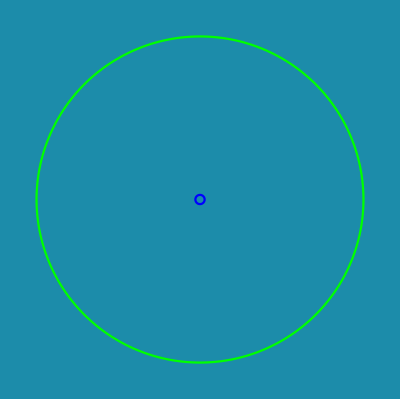

```mathematica
(*Generate a visualization of the configuration*)
Module[{V1=0.005,V2=20,r1,r2},
r1=( Log[1+(V1/Pi)])^(1/2);
r2=( Log[1+((V1+V2)/Pi)])^(1/2);
ParametricPlot[{{r1 Cos[t],r1 Sin[t]},{r2 Cos[t],r2 Sin[t]}},{t, 0,2Pi},Axes->False,PlotStyle->{Blue,Green},Background->RGBColor[0.110, 0.549, 0.667]]]
```

```mathematica
(*Computes weighted surface area for 3D bubble-in-bubble configuration*)
surf3d[V1_,V2_]:=Module[{r1, r2,surf},
r1=r/.FindRoot[Integrate[4Pi r^2 ⅇ^(r^2),r]==V1,{r,0.01}];
r2=r/.FindRoot[Integrate[4Pi r^2 ⅇ^(r^2),r]==V2+V1,{r,0.01}];
surf=4Pi(r1^2ⅇ^(r1^2)+r2^2ⅇ^(r2^2));
Return[{surf,r1, r2}]]
```

```mathematica
surf3d[.005,20]
```

{83.1751,0.105841,1.22052}

```mathematica
(*Generate a visualization of the configuration*)
Module[{V1=0.005,V2=20,r1, r2},
r1=surf3d[V1,V2][[2]];
r2=surf3d[V1,V2][[3]];
SphericalPlot3D[{r1, r2},{θ,0,Pi},{ϕ,0,2Pi},PlotStyle->{Directive[Opacity[0.9],Blue],Directive[Opacity[.5],Green]},Mesh->None, Boxed->False,Axes->False,PlotPoints->100,Background->RGBColor[0.110, 0.549, 0.667]]]
```

-Graphics3D-